```mathematica
dataxy=Import["/home/dnaneet/Research/Dissertation/reconstructing_interpolating_function/testxy.mat"];
datat=Import["/home/dnaneet/Research/Dissertation/reconstructing_interpolating_function/testt.mat"];
Dimensions[dataxy]
Dimensions[datat]
Flatten[datat];
```

{31,31,329}

{1,329,1}

This is how data is plotted. Pay particular emphasis to Flatten[datat]

```mathematica
L=23.659;
datasol=ListInterpolation[dataxy,{{0,L},{0,L},Flatten[datat]}];
Plot3D[datasol[x,y,1000000],{x,0,L},{y,0,L}]

trup=Ceiling[0.35Dimensions[dataxy][[3]]];

profileRup=ListPlot3D[dataxy[[All,All,trup]],BaseStyle->{FontWeight->"Plain",FontSize->25},ColorFunction->Gray,PlotRange->{Full,Full,{0.0,1.5}}]
```

-Graphics3D-

-Graphics3D-

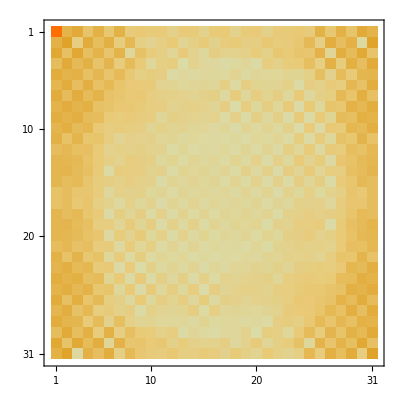

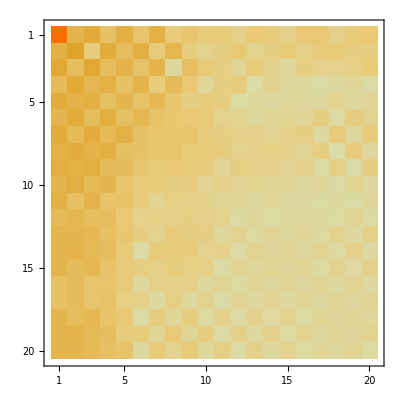

```mathematica
FData=Abs[Fourier[dataxy[[All,All,150]]]];
MatrixPlot[FData]
MatrixPlot[FData⟦1;;20,1;;20⟧]
```

```mathematica
NIntegrate[datasol[x,y,1200000],{x,0,L},{y,0,L}]
```

1.84715×10^40

```mathematica
Max[Flatten[datat]]
```

1.15336×10^6

```mathematica
For[
time=1,time<=Max[Flatten[datat]],time++,
If[
(NIntegrate[datasol[x,y,time],{x,0,L},{y,0,L}]-NIntegrate[datasol[x,y,1],{x,0,L},{y,0,L}])*100/NIntegrate[datasol[x,y,1],{x,0,L},{y,0,L}]<0.0000001,
TRup=time
]
]
```

```mathematica
TMax=12500*100;
TRup=Max[Flatten[datat]];
Plot3D[datasol[x,y,0.95TRup],{x,0,L},{y,0,L}]
```

-Graphics3D-